```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
```

## balanced vs. unbalanced effectors

### plot

```mathematica
pointList={};
```

```mathematica
maxEList={0.166667,0.333333,0.5,0.666667,0.833333,1.};
```

```mathematica
gki=10;
```

```mathematica
For[i=1,i<=Length[maxEList],i++,

thisData=Import["data_balanceTest//zar1_balanceTest_gki_"<>ToString[gki]<>"_maxE_"<>ToString[maxEList[[i]]]<>"_ra.mx"];
AppendTo[pointList,thisData[[1]]]
]
```

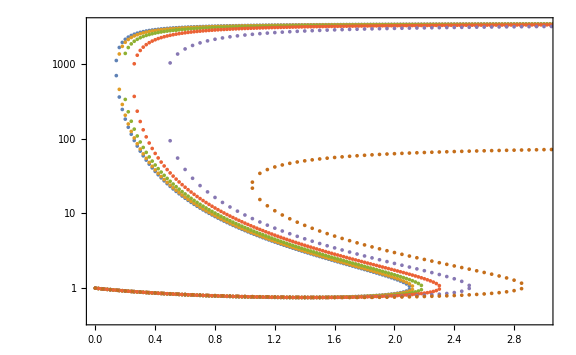

```mathematica
ListLogPlot[pointList,Frame->{True,True,False,False},(*FrameLabel->{"Total effector load ∑_i E_1","Steady-state NLR concentration"},*)LabelStyle->Directive[Black,15],ImageSize->Large,(*PlotLegends->SwatchLegend[{"1/6","2/6","3/6","4/6","5/6","1"},LegendLabel->"E_1/E_T"],*)PlotRange->{{0,3},Automatic},ImageSize->Large]
```

```mathematica
(*Export["zar1_balanceTest_bifurcationIllustration_gki_"<>ToString[gki]<>".png",%,ImageResolution->200]*)
```

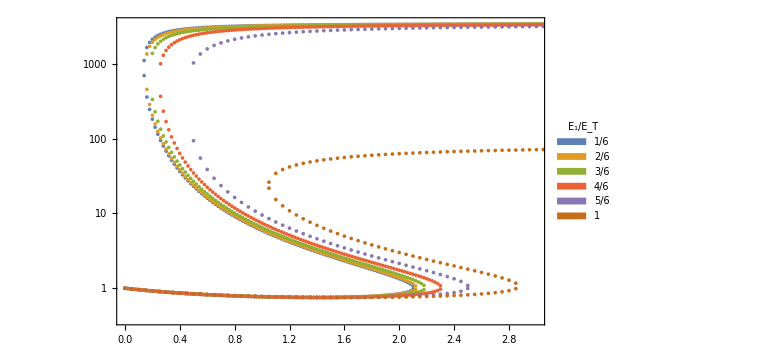

```mathematica
ListLogPlot[pointList,Frame->{True,True,False,False},(*FrameLabel->{"Total effector load ∑_i E_1","Steady-state NLR concentration"},*)LabelStyle->Directive[Black,15],ImageSize->Large,PlotLegends->SwatchLegend[{"1/6","2/6","3/6","4/6","5/6","1"},LegendLabel->"E_1/E_T"],PlotRange->{{0,3},Automatic}]
```

```mathematica
(*Export["zar1_balanceTest_bifurcationIllustration_gki_"<>ToString[gki]<>"_legend.png",%,ImageResolution->200]*)
```

### get threshold and plot

```mathematica
(*determine the transition from 3 fixed points to 1 and return the location of 1 FP*)
getThreshold[inputCoords_]:=Module[{xList,xTally,sortedTally,thresholdFound,i,threshold},

xList=inputCoords[[;;,1]];
xTally=Tally[xList];
sortedTally=SortBy[xTally,First];
thresholdFound=False;
i=2;
threshold="error";
While[(thresholdFound==False)&&(i<=Length[sortedTally]),

If[(sortedTally[[i,2]]==1)&&(sortedTally[[(i-1),2]]>1),threshold=sortedTally[[i,1]];
thresholdFound=True;
,
i=i+1;
];

];

threshold

]
```

```mathematica
(*loop and plot*)
```

```mathematica
gkList={10,5,2};
```

```mathematica
e1FractionList={0.166667,0.333333,0.5,0.666667,0.833333,1.};
```

```mathematica
allData={};
```

```mathematica
For[i=1,i<=Length[gkList],i++,

thisPointList={};
For[j=1,j<=Length[e1FractionList],j++,


thisData=Import["data_balanceTest//zar1_balanceTest_gki_"<>ToString[gkList[[i]]]<>"_maxE_"<>ToString[e1FractionList[[j]]]<>"_ra.mx"][[1]];

thisThreshold=getThreshold[thisData];
AppendTo[thisPointList,{e1FractionList[[j]],thisThreshold}]
];

AppendTo[allData,thisPointList];

]
```

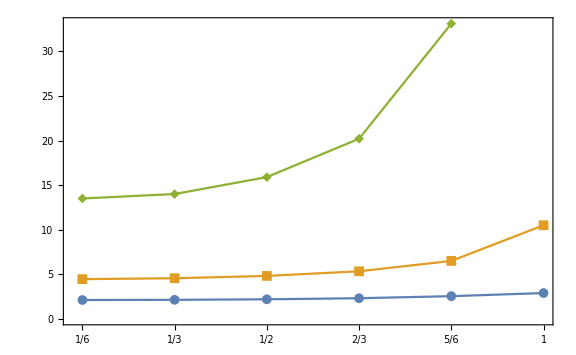

```mathematica
ListPlot[allData,Frame->{True,True,False,False},LabelStyle->Directive[Black,15],ImageSize->Large,PlotMarkers->{Automatic,Medium},Joined->True,FrameTicks->{{1/6,2/6,3/6,4/6,5/6,6/6},Automatic}]
```

```mathematica
(*Export["zar1_balance_thresholdPlot.png",%,ImageResolution->200]*)
```

zar1_balance_thresholdPlot.png

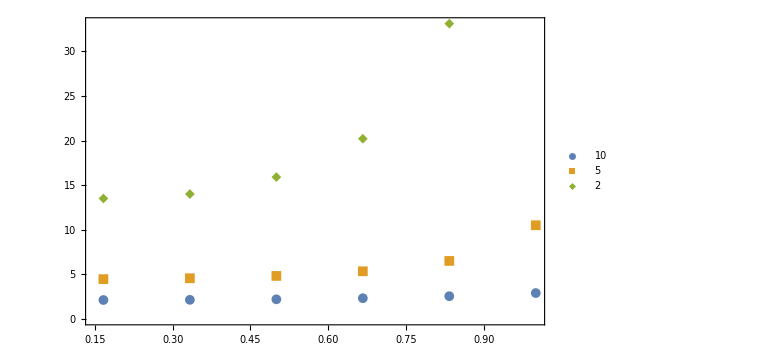

```mathematica
ListPlot[allData,Frame->{True,True,False,False},LabelStyle->Directive[Black,15],ImageSize->Large,PlotLegends->{"10","5","2"},PlotMarkers->{Automatic,Medium}]
```

```mathematica
(*Export["zar1_balance_thresholdPlot_legend.png",%,ImageResolution->200]*)
```

zar1_balance_thresholdPlot_legend.png